# Images Generation

## Data loading

```mathematica
ResultPerRunPeriodicData=Import[NotebookDirectory[]<>"Data\\modelo_periodic_100.m"];
```

```mathematica
dataPeriodic=Around[Mean[#],StandardDeviation[#]]&/@Transpose[Map[Mean[#]&,Values[Transpose[ResultPerRunPeriodicData[[All,All,3]]]]]];
```

```mathematica
ResultPerRunStaticData=Import[NotebookDirectory[]<>"Data\\modelo_convergente_100.m"];
```

```mathematica
dataStatic=Around[Mean[#],StandardDeviation[#]]&/@Transpose[Map[Mean[#]&,Values[Transpose[ResultPerRunStaticData[[All,All,3]]]]]];
```

```mathematica
ResultPerRunChaoticData=Import[NotebookDirectory[]<>"Data\\modelo_caotico_100.m"];
```

```mathematica
dataChaotic=Around[Mean[#],StandardDeviation[#]]&/@Transpose[Map[Mean[#]&,Values[Transpose[ResultPerRunChaoticData[[All,All,3]]]]]];
```

```mathematica
ResultPerRunComplexData=Import[NotebookDirectory[]<>"Data\\modelo_complejo_100.m"];
```

```mathematica
dataComplex=Around[Mean[#],StandardDeviation[#]]&/@Transpose[Map[Mean[#]&,Values[Transpose[ResultPerRunComplexData[[All,All,3]]]]]];
```

## Plots implementation

```mathematica
plot1=ListPlot[{dataStatic,dataPeriodic},PlotRange->{{0,4.5},{0.04,0.2}},Frame->True,FrameTicks->{{All,None},{{{1,"G_up"},{2,"G_down"},{3,"G_right"},{4,"G_left"}},None}},PlotStyle->{PointSize[10^-1.5]},PlotLegends->Placed[{"Convergent","Periodic"},Below],ImageSize->Full];
```

```mathematica
plot2=ListPlot[{dataChaotic,dataComplex},PlotRange->{{0,4.5},{0.9,1}},Frame->True,FrameTicks->{{Range[0.9,1,0.02],None},{{{1,"G_up"},{2,"G_down"},{3,"G_right"},{4,"G_left"}},None}},PlotStyle->{PointSize[10^-1.5]},PlotLegends->Placed[{"Chaotic","Complex"},Below],ImageSize->Full];
```

```mathematica
finaplot=ListPlot[{dataStatic,dataPeriodic,dataComplex,dataChaotic},PlotRange->{{0.4,4.5},All},FrameLabel->{None,Style["Bits",25]},Frame->True,FrameTicks->{{All,None},{{{1,"G_up"},{2,"G_down"},{3,"G_right"},{4,"G_left"}},None}},PlotStyle->{PointSize[10^-1.7]},PlotLegends->Placed[{Style["Convergent",25],Style["Periodic",25],Style["Complex",25],Style["Chaotic",25]},{Below,Center}],ImageSize->Medium,AspectRatio->1.2,PlotMarkers->{"OpenMarkers",15},ImageSize->Full, FrameTicksStyle->25,FrameStyle->Thick];
```

```mathematica
finalplot=Show[finaplot,ImageSize->700]
```

-Graphics-

```mathematica
Export[NotebookDirectory[]<>"Images\\final_plot_4.jpg",finalplot];
```

```mathematica
colors={RGBColor[0.560181,0.691569,0.194885],RGBColor[0.922526, 0.385626, 0.209179]}
```

{RGBColor[0.560181, 0.691569, 0.194885],RGBColor[0.922526, 0.385626, 0.209179]}

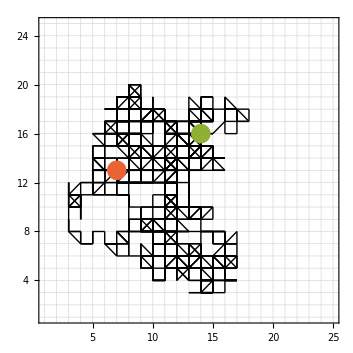

```mathematica
ComplexDataRaw2=Import[NotebookDirectory[]<>"Data\\modelo_complejo_1.csv","Data"];
data1=ComplexDataRaw2[[8;;]][[All,{3,4}]];
imagecomplex=Graphics[{{White,PointSize[10^-3],Point[{1,1}],Point[{25,25}]},Line/@(Partition[#,2,1]&@(data1)),PointSize[10^-1.4],{colors[[1]],Point[data1[[1]]]},{colors[[2]],Point[data1[[-1]]]}},GridLines->{Range[0,30],Range[0,30]},Frame->True]
```

```mathematica
Export[NotebookDirectory[]<>"Images\\complex_rw.png",imagecomplex]
```

C:\Users\sebas\OneDrive\Tesis\Images\complex_rw.png

```mathematica
ChaosWalkRaw=Import[NotebookDirectory[]<>"Data\\modelo_caotico_1.csv","Data"];
ChaosWalk=ChaosWalkRaw[[8;;]][[All,{3,4}]];
```

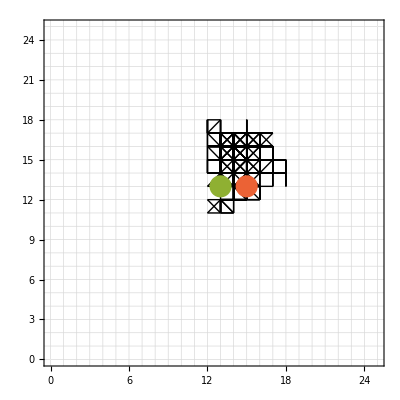

```mathematica
imgchaos=Graphics[{{White,PointSize[10^-3],Point[{0,0}],Point[{25,25}]},
Line/@(Partition[#,2,1]&@(ChaosWalk)),PointSize[10^-1.4],{colors[[1]],Point[ChaosWalk[[1]]]},{colors[[2]],Point[ChaosWalk[[-1]]]}
},Frame->True,GridLines->{Range[0,30],Range[0,30]}]
```

```mathematica
Export[NotebookDirectory[]<>"Images\\chaos_rw.png",imgchaos]
```

C:\Users\sebas\OneDrive\Tesis\Images\chaos_rw.png

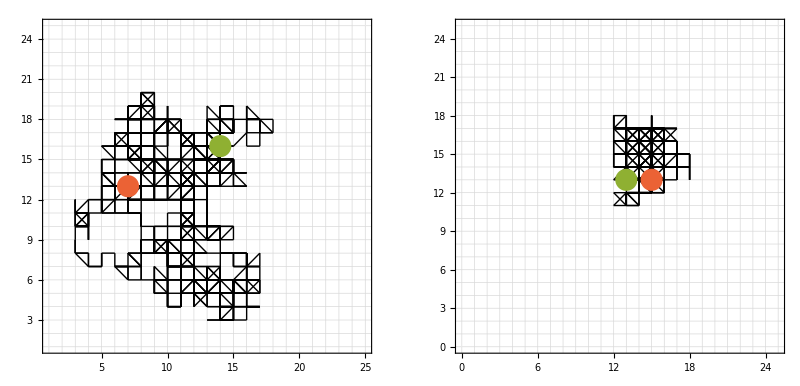

```mathematica
rw=GraphicsRow[{imagecomplex,imgchaos}]
```

```mathematica
Export[NotebookDirectory[]<>"Images\\rw3.png",rw]
```

C:\Users\sebas\Desktop\Documentos\Github\OneDrive\Tesis\Images\rw3.png